```mathematica
ClearAll["Global`*"]
```

```mathematica
xl=0;
xr=1;
```

```mathematica
(*test case 1*)
```

```mathematica
u[x_]:=Cos[2π x/(xr-xl)]/(1+Cos[2π x/(xr-xl)]^4)
```

```mathematica
u[x]//FullSimplify
```

1/(Cos[2 π x]^3+Sec[2 π x])

```mathematica
u'[x]//FullSimplify
```

(2 π (-1+3 Cos[2 π x]^4) Sin[2 π x])/((1+Cos[2 π x]^4)^2)

```mathematica
u''[x]//FullSimplify
```

(π^2 Cos[2 π x] (-187+344 Cos[4 π x]+388 Cos[8 π x]-24 Cos[12 π x]-9 Cos[16 π x]))/(32 (1+Cos[2 π x]^4)^3)

```mathematica
(*check for u*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/solution/nodal_values/u.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]]]],{i,1,Length[t]}]]
```

1.78178×10^-7

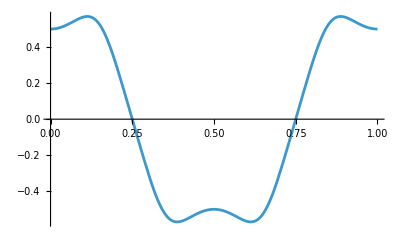

```mathematica
plotexact=Plot[u[x],{x,xl,xr},PlotRange->Full]
```

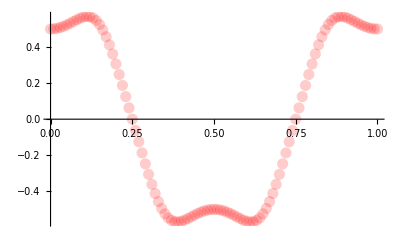

```mathematica
plotnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[0.2],PointSize->0.02}]
```

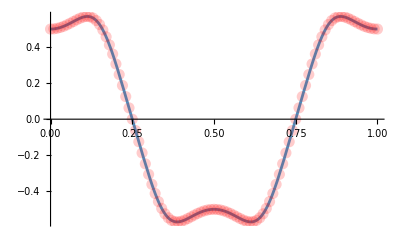

```mathematica
Show[plotexact,plotnum]
```